```mathematica
SetDirectory[NotebookDirectory[]];
```

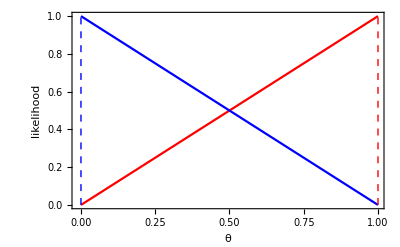

```mathematica
gFinal=Plot[{θ,1-θ},{θ,0,1},PlotStyle->{Red,Blue},Frame->{True,True,False,False},BaseStyle->Medium,FrameLabel->{"θ","likelihood"},PlotRange->{{-0.01,1},{0,1}},Epilog->{{Red,Dashed,Line[{{1,0},{1,1}}]},{Blue,Dashed,Line[{{0,0},{0,1}}]}}]
```

```mathematica
Export["Distributions_bernoulliHorseRace.pdf",gFinal]
```

Distributions_bernoulliHorseRace.pdf

```mathematica
Binomial[10,5]
```

252